```mathematica
file="勾.svg";
```

```mathematica
data=Import[NotebookDirectory[]<>"/"<>file,"Text"];
```

## 格式处理

### 结构拆分

```mathematica
GetAllGroups[str_]:=StringCases[str,Shortest["<g"~~string:___~~"</g>"]:>"<g"<>string<>"</g>"]
```

```mathematica
GetAllPath[str_]:=StringCases[str,Shortest["<path id=\""~~id:___~~"\" class=\""~~class:___~~"\" d=\""~~string:___~~"\""~~___~~"/>"]:>string]
GetAllPolyLine[str_]:=StringCases[str,{Shortest["<polyline id=\""~~id:___~~"\" class=\""~~class:___~~"\" points=\""~~string:___~~"\"/>"]:>string}]
GetAllLine[str_]:=StringReplace[StringCases[str,Shortest["<line id=\""~~id:___~~"\" class=\""~~class:___~~"\" "~~path:___~~"/>"]:>path],{"\""->"","x1="->"","y1="->"","x2="->"","y2="->""," "->","}]
GetMarks[group_]:=GetAllLine[group]~Join~GetAllPolyLine[group]
```

### 清理字符串

```mathematica
AddComma[str_]:=StringReplace[str,{"-"->",-",Whitespace..->",",L:LetterCharacter:>","<>L<>","}]
```

```mathematica
CleanString[str_]:=StringReplace[StringReplace[StringReplace[AddComma@str,{Whitespace->","}],{","..:>","}],{(PunctuationCharacter~~EndOfString):>"",StartOfString~~","..->""}]
```

### 控制点处理

格式化字串：

```mathematica
GetControlPoints[str_]:=ToExpression/@Flatten[StringCases[str,{Shortest[L:LetterCharacter~~","~~num:___~~","~~Ln:LetterCharacter]:>"{\""<>L<>"\",{"<>num<>"}}"},Overlaps->True]]
```

得到贝塞尔曲线控制点序列：

```mathematica
GetBezierData[rawData_]:=Module[{currentPoint={0,0},currentControl,list={},c1={0,0},c2={0,0}},
Do[
{c1,c2,currentPoint}=Switch[rawData⟦i,1⟧,
"M",{c1,c2,currentPoint+rawData⟦i,2⟧},
"c",{currentPoint+rawData⟦i,2,1;;2⟧,currentPoint+rawData⟦i,2,3;;4⟧,currentPoint+rawData⟦i,2,5;;6⟧},
"C",{rawData⟦i,2,1;;2⟧,rawData⟦i,2,3;;4⟧,rawData⟦i,2,5;;6⟧},
"s",{currentPoint-(c2-currentPoint),currentPoint+rawData⟦i,2,1;;2⟧,currentPoint+rawData⟦i,2,3;;4⟧},
"S",{currentPoint-(c2-currentPoint),rawData⟦i,2,1;;2⟧,rawData⟦i,2,3;;4⟧},
"l",{currentPoint,c2+rawData⟦i,2⟧,currentPoint+rawData⟦i,2⟧},
"L",{currentPoint,rawData⟦i,2⟧,rawData⟦i,2⟧},
"h",{currentPoint,{currentPoint⟦1⟧+rawData⟦i,2,1⟧,currentPoint⟦2⟧},{currentPoint⟦1⟧+rawData⟦i,2,1⟧,currentPoint⟦2⟧}},
"H",{currentPoint,{rawData⟦i,2,1⟧,currentPoint⟦2⟧},{rawData⟦i,2,1⟧,currentPoint⟦2⟧}},
"v",{currentPoint,{currentPoint⟦1⟧,currentPoint⟦2⟧+rawData⟦i,2,1⟧},{currentPoint⟦1⟧,currentPoint⟦2⟧+rawData⟦i,2,1⟧}},
"V",{currentPoint,{currentPoint⟦1⟧,rawData⟦i,2,1⟧},{currentPoint⟦1⟧,rawData⟦i,2,1⟧}}
];
AppendTo[list,{c1,c2,currentPoint}]
,{i,1,Length[rawData]}];
list
]
```

### 坐标转换

```mathematica
SVGToMMA[points_]:=RotationTransform[π]/@ReflectionTransform[{1,0}]/@points
```

### 数据绘图

```mathematica
BezierPlot[points_,color_:Hue[1,0.7,0.7,0.5]]:=Graphics[{color,FilledCurve@BezierCurve[SVGToMMA@#⟦3;;⟧]&/@(points)}]
```

## 从原始数据获得所有训练数据

```mathematica
GetTrainData[xml_]:=Module[
{paths,marks,groups=GetAllGroups[data],groupnumber},
groupnumber=Length[groups];
paths=CleanString/@(GetAllPath/@groups);
marks=ToExpression@ToString[CleanString/@(GetMarks/@groups)];

paths=Flatten[#,1]&/@#&/@Map[GetBezierData,Map[GetControlPoints,paths,{2}],{2}];
<|"Path"->paths,"Mark"->marks|>
]
```

## 测试

```mathematica
Length/@#&/@GetTrainData[data]["Path"]
```

{{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39},{27,39}}

```mathematica
BezierPlot[GetTrainData[data]["Path"]⟦30⟧]
```

-Graphics-

{{{0,0},{0,0},{1,1}},{{1,2},{2,1},{2,2}},{{2,3},{5/2,2},{3,3}},{{7/2,4},{5,3},{4,4}},{{3,5},{-1,0},{1,1}},{{1,1},{2,1},{2,1}},{{2,1},{3,1},{3,1}},{{3,1},{3,2},{3,2}},{{3,2},{4,2},{4,2}},{{4,2},{4,0},{4,0}}}

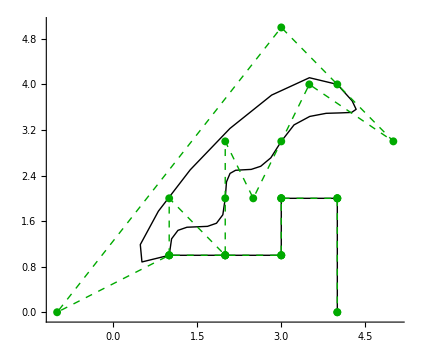

```mathematica
b=GetBezierData[{{"M",{1,1}},{"c",{0,1,1,0,1,1}},{"c",{0,1,1/2,0,1,1}},{"s",{2,0,1,1}},{"S",{-1,-0,1,1}},{"h",{1}},{"H",{3}},{"v",{1}},{"h",{1}},{"V",{0}}}]
Graphics[{Thick,BezierCurve[Flatten[b,1]⟦3;;⟧],Dashed,Darker@Green,Line[Flatten[b,1]⟦3;;⟧],Disk[#,0.07]&/@(Flatten[b,1]⟦3;;⟧)},Axes->True]
```

```mathematica
b2=Flatten[#,1]⟦3;;⟧&/@(GetBezierData/@GetControlPoints/@CleanString@GetAllPath[GetAllGroups[data]⟦8⟧]);
b2=(RotationTransform[π]/@#&)/@b2;
b2=(ReflectionTransform[{1,0}]/@#&)/@b2;
Graphics[{EdgeForm[{Thick,Gray}],FaceForm[Black],FilledCurve@BezierCurve[#,SplineClosed->True]&/@b2,Dashed,Darker@Green,Line/@b2,Disk[#,0.1]&/@#&/@b2},Axes->True,AspectRatio->Automatic]
```

-Graphics-

```mathematica
CleanString@GetAllPath[GetAllGroups[data]⟦2⟧]
```

{M,143.88,53.38,c,1,0.24,1.23,0.64,0.91,1.19,s,-2.11,2.12,-3.5,3.11,c,-1.39,0.99,-5.34,2.84,-5.67,2.7,c,-0.33,-0.14,0.04,-0.47,0.37,-0.65,c,0.33,-0.18,1.9,-1.32,2.93,-2.41,c,1.02,-1.1,2.19,-2.45,2.23,-2.89,c,0.04,-0.44,-0.44,-0.92,0.22,-1.05,C,142.01,53.26,143.34,53.26,143.88,53.38,z,M,142.71,55.82,c,0.31,-0.42,2.45,0.04,4.86,-0.55,c,2.41,-0.59,4.68,-1.32,5.56,-1.17,s,2.27,1.28,2.45,1.72,c,0.18,0.44,-1.39,10.75,-1.76,12.25,c,-0.37,1.5,-2.16,4.24,-3.18,4.2,c,-1.02,-0.04,-3.51,-3.55,-3.51,-3.8,s,2.23,0.18,2.6,0.07,s,1.57,-3.16,2.01,-5.37,c,0.44,-2.2,0.59,-7.03,0.33,-7.21,c,-0.26,-0.18,-3.25,0.65,-4.75,0.87,s,-3.25,0.41,-3.91,0.3,C,142.74,57.03,142.49,56.11,142.71,55.82,z}

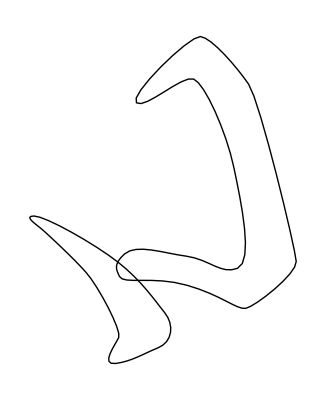

```mathematica
Graphics[BezierCurve@Flatten[#,1]⟦3;;⟧&/@(GetBezierData/@GetControlPoints/@CleanString@GetAllPath[GetAllGroups[data]⟦29⟧])]
```

```mathematica
GetControlPoints@CleanString@GetAllPath[GetAllGroups[data]⟦4⟧]
```

{{M,{238.89,139.26}},{c,{0.99,0.09,7.98,-1.61,8.4,-1.65}},{c,{0.43,-0.05,1.18,-0.14,1.18,0.57}},{s,{-0.14,4.58,-0.66,6.47}},{s,{-1.84,4.98,-1.84,4.98}},{l,{-3.87,-0.49}},{c,{0,0,2.93,3.68,3.87,3.73}},{s,{2.55,-1.99,3.07,-3.24}},{s,{1.61,-8.19,2.03,-8.9}},{c,{0.43,-0.71,0.47,-1.94,-0.24,-2.93}},{s,{-0.61,-2.46,-1.65,-2.36}},{s,{-4.16,1.09,-6.05,1.51}},{c,{-1.89,0.43,-4.96,1.18,-4.96,1.18}},{s,{0.14,-0.14,0,-0.85}},{s,{-0.24,-1.23,-0.76,-1.23}},{c,{-0.52,0,-1.89,0,-2.13,0.33}},{s,{0.47,0.38,0.33,0.8}},{c,{-0.14,0.43,-0.61,1.37,-2.31,2.5}},{s,{-3.87,2.55,-3.83,2.83}},{c,{0.05,0.28,2.6,-0.47,3.83,-1.13}},{s,{3.92,-2.22,3.92,-2.22}},{L,{238.89,139.26}}}

```mathematica
CleanString@GetAllPolyLine[GetAllGroups[data]⟦3⟧]
```

{235.54,48.86,246.74,49.24,243.81,70.74}

```mathematica
StringReplace["235.54,48.86,246.74,49.24,243.81,70.74,",","~~EndOfString->""]
```

235.54,48.86,246.74,49.24,243.81,70.74